同じ形にするための式変形

```mathematica
Simplify[Sin[a]^2 Cosh[a]^2+Cos[a]^2 Sinh[a]^2==(Cosh[2 a]-Cos[2a])/2]
```

True

```mathematica
Simplify[Sin[a]Cos[a]+Sinh[a]Cosh[a]==(Sin[2a]+Sinh[2a])/2]
```

True

```mathematica
Simplify[Sin[a]Cos[a]-Sinh[a]Cosh[a]==(Sin[2a]-Sinh[2a])/2]
```

True

結果をそのまま打ち込んで書いたグラフ

1.69577×10^-15 √((-0.000626657 √(f^2) (6.46814×10^11-4.04842×10^-13 f^2) Cot[0.00021933 √(f^2)]+(498.183 √f (-1.02344 f (Cos[174.352 √f] Sin[174.352 √f]-Cosh[174.352 √f] Sinh[174.352 √f])+(6.46814×10^11-4.04842×10^-13 f^2) (Cos[174.352 √f] Sin[174.352 √f]+Cosh[174.352 √f] Sinh[174.352 √f])))/(Cosh[174.352 √f]^2 Sin[174.352 √f]^2+Cos[174.352 √f]^2 Sinh[174.352 √f]^2))/((6.46814×10^11+4.04842×10^-13 f^2)^2 (225.027 f^2-503.988 √(f^2) Cot[0.00021933 √(f^2)])^2))

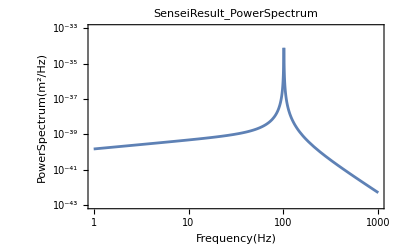

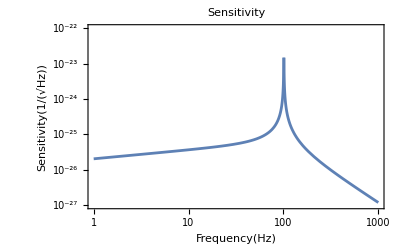

```mathematica
SD=(4kB T)/ω^2(ω s E0)/((M ω^2-s E0 k2 Cot[k2 L])^2) (χ s E0 ω)/(((s E0)^2+(χ ρ ω)^2)^2) (s E0 α^2 T)/Cv(√(ω/(2χ))1/(Sin[kd L]^2 Cosh[kd L]^2+Cos[kd L]^2 Sinh[kd L]^2) ((Sin[kd L]Cos[kd L]+Sinh[kd L]Cosh[kd L])((s E0)^2-(χ ρ ω)^2) - (Sin[kd L]Cos[kd L]-Sinh[kd L]Cosh[kd L])2 χ ρ ω s E0)-k2 Cot[k2 L]((s E0)^2-(χ ρ ω)^2)) /.
{k2->√((ρ ω^2)/(s E0)),kd->√(ω/(2χ)),χ->κ/(ρ Cv)}/.
{kB->1.38 10^-23,T->300,α->5.0*10^(-6),L->0.35,κ->0.00008,ρ->0.008,Cv->7.9 10^2,ω->2π f,E0->4.0*10^(11),M->22.8/4,s->0.0016^2 Pi/4,χ->1.266*10^-5};
Sensi=√SD /200/3000
SDg=LogLogPlot[SD,{f,1,1000},PlotRange->{10^-43,10^-33},PlotLabel->SenseiResult_PowerSpectrum,Frame->True,FrameLabel->{Frequency[Hz],PowerSpectrum[m^2/Hz]}]
SensiG=LogLogPlot[Sensi,{f,1,1000},PlotRange->{10^-27,10^-22} ,PlotLabel->Sensitivity,Frame->True,FrameLabel->{Frequency[Hz],Sensitivity [1/Sqrt[Hz]]}](*Sensitivity*)
```

結果を少し変形して書いたグラフ

1.69577×10^-15 √((-0.000626657 √(f^2) (6.46814×10^11-4.04842×10^-13 f^2) Cot[0.00021933 √(f^2)]+(498.183 √f (-1.02344 f (Sin[348.703 √f]-Sinh[348.703 √f])+(6.46814×10^11-4.04842×10^-13 f^2) (Sin[348.703 √f]+Sinh[348.703 √f])))/(-Cos[348.703 √f]+Cosh[348.703 √f]))/((6.46814×10^11+4.04842×10^-13 f^2)^2 (225.027 f^2-503.988 √(f^2) Cot[0.00021933 √(f^2)])^2))

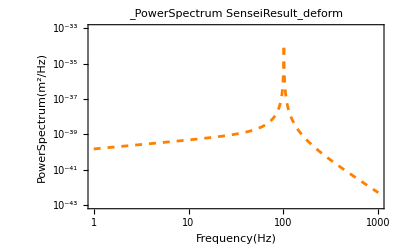

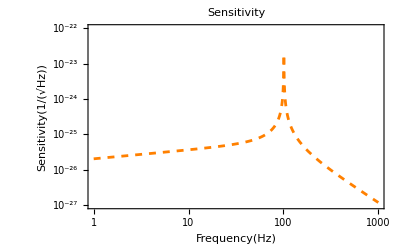

```mathematica
SDd=(4kB T)/ω^2(ω s E0)/((M ω^2-s E0 k2 Cot[k2 L])^2) (χ s E0 ω)/(((s E0)^2+(χ ρ ω)^2)^2) (s E0 α^2 T)/Cv(√(ω/(2χ))1/(Cosh[2kd L] -Cos[2 kd L]) ((Sin[2 kd L]+Sinh[2 kd L])((s E0)^2-(χ ρ ω)^2) - (Sin[2 kd L] - Sinh[2 kd L])2 χ ρ ω s E0)-k2 Cot[k2 L]((s E0)^2-(χ ρ ω)^2)) /.
{k2->√((ρ ω^2)/(s E0)),kd->√(ω/(2χ)),χ->κ/(ρ Cv)}/.
{kB->1.38 10^-23,T->300,α->5.0*10^(-6),L->0.35,κ->0.00008,ρ->0.008,Cv->7.9 10^2,ω->2π f,E0->4.0*10^(11),M->22.8/4,s->0.0016^2 Pi/4,χ->1.266*10^-5};
SensiD=√SDd /200/3000
SDdg=LogLogPlot[SDd,{f,1,1000},PlotRange->{{1,1000},{10^-43,10^-33}},PlotStyle->{Orange,Dashed},PlotLabel->SenseiResult_deform_PowerSpectrum,Frame->True,FrameLabel->{Frequency[Hz],PowerSpectrum[m^2/Hz]}]
SensiDG=LogLogPlot[SensiD,{f,1,1000},PlotRange->{{1,1000},{10^-27,10^-22}},PlotStyle->{Orange,Dashed},PlotLabel->Sensitivity,Frame->True,FrameLabel->{Frequency[Hz],Sensitivity[1/Sqrt[Hz]]}] (*Sensitivity*)
```

```mathematica
LogLogPlot[{Sensi,SensiD},{f,1,1000},PlotRange->{{1,1000},{10^-27,10^-22}},PlotStyle->{Thick,{Orange,Dashed}},PlotLegends->Placed[{"sensei","deform_ver"},{0.3,0.7}],PlotLabel->Sensitivity,Frame->True,FrameLabel->{Frequency[Hz],Sensitivity[1/Sqrt[Hz]]}]
```